0.5

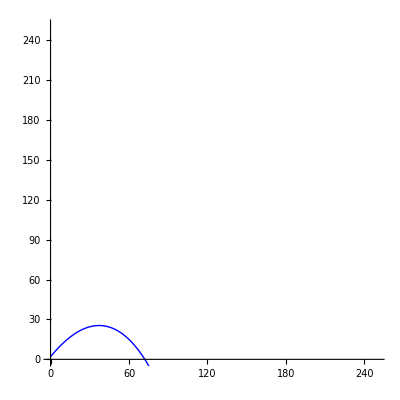

```mathematica
(*example from class*)
g = 9.8;
l = 0.5
c = 3 10^8;
m = 1;
vt = Sqrt[m g/c];
V = 30;
th = 50 Pi/180;

sol =
With[{vt=50},
NDSolve[{x''[t]== (-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2], y''[t]==-g (1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]),{x[0]==0,y[0]==2},{x'[0]==V Cos[th], y'[0]==V Sin[th]}}, {x,y},{t,0,200}]];
myplot = ParametricPlot[Evaluate[{x[t],y[t]}/.sol], {t,0,200}, PlotStyle-> RGBColor[0,0,1], PlotRange-> {0,250}];
Show[myplot]
```

```mathematica
(*excersize from class*)
g=9.81
Manipulate[Module[{sol=NDSolve[{x''[t]==(-g x'[t]/vterm^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g (1+(y'[t]/vterm^2) Sqrt[x'[t]^2+y'[t]^2]),{y[0]==y0,x[0]==0},{y'[0]==V Sin[theta],x'[0]==V Cos[theta]}},{x,y},{t,0,200}]},ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],{V Cos[theta] t,y0+V Sin[theta] t-0.5 g t^2}},{t,0,tf},PlotRange->{{0,500},{0,1000}}]],{{y0,0,"Initial Height (m)"},10,1000,Appearance->"Labeled"},{{V,10,"Initial Velocity (m/s)"},10,200,Appearance->"Labeled"},{{vterm,10,"Terminal Velocity (m/s)"},20,200,Appearance->"Labeled"},{{theta,0.1,"Initial Angle (rad)"},.1,Pi/2,Appearance->"Labeled"},{{tf,1,"Time (s)"},1,30,Appearance->"Labeled"}]
```

9.81

```mathematica
(*cannon ball code. for some reason I can't get the graphs to show up even though it will let me manipulate the individual values*)
Manipulate[
Module[
{sol=With[{vt=Sqrt[2 m 9.8/(.5 1.29 a)]},
NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g(1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]),{x[0]==0,y[0]==2},{x'[0]==V Cos[theta], y'[0]==V Sin[theta]}},{x,y},{t,0,200}]]},
ParametricPlot[{Evaluate[x[t],y[t]/.sol], {V Cos[theta] t,y0+V Sin[theta] t,y0+V Sin[theta]t-0.5 g t^2}}, {t,0,tf},AxesLabel-> {"x (m)", "y (m)"}, PlotRange-> {{0,150},{0,150}},ImageSize->{500,300}]],
{{a,0.001,"Area (m^2)"},0.001,1,Appearance->"Labeled"},
{{m,0.01,"mass (kg)"},0.01,3,Appearance->"Labeled"},
{{y0,0,"initial height (m)"},0,3,Appearance-> "Labeled"},
{{V,10,"initial valocity (m/s)"},10,200,Appearance->"Labeled"},
{{theta,0.1,"initial anagle (rad)"},0.1,Pi/2,Appearance->"Labeled"},
{{tf,0.01,"time (s)"}, 0.01,20.,Appearance->"Labeled"}]
```